Método de la secante

Proyecto Métodos Numéricos.
Theodoro Thair Salas López
S18019554

Como ejemplo se resolverá la ecuación f(x) = x - Cos (x). Se debe especificar un intervalo para poder aproximar la derivada como una razón de cambio. las especificaciones sobre el método se encuentran en el reporte.

```mathematica
a= -1; b=1;
```

```mathematica
f[x_]:=x-Cos[x]
```

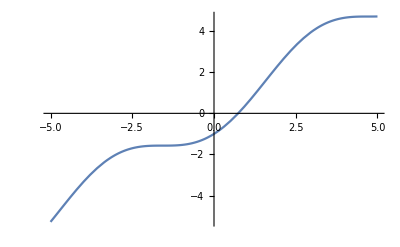

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
MatrixForm[Table[{x,f[x]},{x,-5,5}]]
```

(-5 | -5-Cos[5]
-4 | -4-Cos[4]
-3 | -3-Cos[3]
-2 | -2-Cos[2]
-1 | -1-Cos[1]
0 | -1
1 | 1-Cos[1]
2 | 2-Cos[2]
3 | 3-Cos[3]
4 | 4-Cos[4]
5 | 5-Cos[5])

Existe un cambio de signo entre[-1, 1].

```mathematica
While[True,{
x=(b*f[a]-a*f[b])/(f[a]-f[b]);
If[Abs[f[x]]<10^-6,Break[],{a=b;b=x}]
}]
```

```mathematica
Print[N[{x,f[x]}]];
```

{0.739085,-2.66741×10^-10}

Se puede decir que en x = 0.739085 se encuentra la raíz de la función f(x) = x - Cos(x).